```mathematica
NestSymbFunc[symbFunc_, n_, var_:x]:=Quiet[ReplaceRepeated[symbFunc, var->symbFunc, MaxIterations->n-1], ReplaceRepeated::rrlim]
SymbToFunc[symbFunc_, var_:x]:=Function[{dontusethisvariable},(symbFunc)/.{var->dontusethisvariable}]
SymbToFunc[symbFunc_List, var_:x]:=SymbToFunc[#, var]&/@symbFunc
```

r+s x

a+b x

{a→2,b→3}

Nested testForm:

r+r s+s^2 x

Coefficients:

{Coefficients:}

{a,b}

{r+r s,s^2}

{r,s}

Solutions:

{{r→(-a-a √b)/(-1+b),s→-√b},{r→(-a+a √b)/(-1+b),s→√b}}

Iterate Form:

(-a-a √b)/(-1+b)-√b x

Target:

a+b x

Simplifications of iterate:

-a/(-1+b)+(a b)/(-1+b)+b x

-a/(-1+b)+(a b)/(-1+b)+b x

a+b x

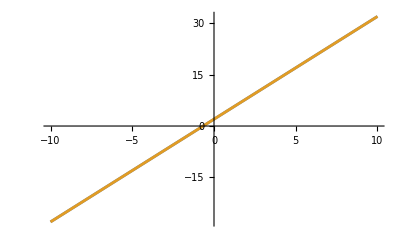

```mathematica
testForm=r+s x
targetForm=a +b x
testValues={a->2,b->3}

"Nested testForm:"
nestedTestForm=NestSymbFunc[testForm,2]

"Coefficients:"
CoefficientList[%,x]
targetList=CoefficientList[targetForm,x]
nestedTestList=CoefficientList[nestedTestForm,x]
vars=CoefficientList[testForm,x]

"Solutions:"
sol=Solve[targetList==nestedTestList,(vars)]

"Iterate Form:"
iterateSymb=testForm/. First[sol]

"Target:"
targetForm

"Simplifications of iterate:"
NestSymbFunc[iterateSymb,2]
ExpandAll@%
FullSimplify@%

targetFunc=SymbToFunc[targetForm/. testValues];
testFunc=SymbToFunc[NestSymbFunc[iterateSymb,2]/. testValues];

Plot[{targetFunc[x],testFunc[testFunc[x]]},{x,-10,10}]
```